# Find the GW modes for each planet. Calculate SNR with Bill’s summation over modes and time T (following Maggiore analysis).

## Load the GW functions, mostly from Maggiore chapter 4.

```mathematica
(*Needs["GWFormulae.nb`"]*)
(*Once[ Get["GWFormulae.nb"] ]*)  (* Once insures it is read only once. *)
(*Import["GWFormulae.nb"]*)
NotebookEvaluate["GWFormulae.nb"]  (* This works, does spit out the tests and evaluations along the way in the Notebook.  Either comment them out or put up with output. *)
```

The eccentricy and mode dependent power factor called g(n,e) in Maggiore's Eqn. 4.108, note the semi-major axis "a" cancels out of the numerator and denominator.

The frequency in Hz of the binary given the two masses m1, m2, and the semi-major axis a.

Given the exop data table aa and the index to check for blanks filterInd, returns the two lists of non-blank data and black data in that field.

The coefficient in front of the power formulae, especially Maggiore's Eqns. 4.107 (and 4.74).

Given the data table and a string in the header row, returns the header row.  Default string is "pl_hostname" .

```mathematica
?getNmax
```

The approximate mode index n-star where the power curve falls down to 0.05 of the maximum value of the curve.

```mathematica
?fr
```

The frequency of the orbit in Hz given the two masses m1, m2, and the semimajor axis a.

```mathematica
fr[1.0*massE, 1.0*massSun, 1.0*au]*3.1 10^7
```

0.982651

## Read CVS File

```mathematica
thisDir = NotebookDirectory[];
csvDir = thisDir <>"dbases/";
pixDir = thisDir <>"pix/";
csvFileName = csvDir <> "exop_20180201_092937.csv"
```

/home/gabella/Documents/astro/exop/exoplanetsMath/dbases/exop_20180201_092937.csv

```mathematica
exopDateTime = dateTimeStamp[csvFileName]
```

20180201_092937

### Grab all the rows in the csv file.

```mathematica
alldata = Import[csvFileName, "Data"];
```

```mathematica
Length[alldata]
```

3589

Test which row has the headers in it, starting at row 1.  Return -999 if there is no element “pl_hostname” at the [[n,1]] position.

```mathematica
rowHeaders = findHeaderRow[alldata]
rowDataStart = rowHeaders+1;
{rowHeaders, rowDataStart}
```

1

{1,2}

### Make the dictionary of column names with createCols[] .

```mathematica
cols = createCols[alldata, rowHeaders]
```

<|pl_hostname→1,pl_letter→2,pl_discmethod→3,pl_orbper→4,pl_orbsmax→5,pl_orbeccen→6,pl_bmassj→7,st_dist→8,st_mass→9,rowupdate→10,st_plx→11|>

```mathematica
{cols["pl_hostname"], cols["st_mass"]}
```

{1,9}

### Filter the data, we need distance, both masses, and the semi-major axis of the orbit to be non-zero for our calculations.

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.

```mathematica
Print["Using database from ", exopDateTime, ".  Length alldata ",Length[alldata] ]
tempdata = alldata;
tempdata= filterBlanks[tempdata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "Number with pl_orbeccen ", Length[tempdata]]
tempdata= filterBlanks[tempdata, cols["pl_orbper"] ][[1]]; Print[ "Number with pl_orbper ",Length[tempdata] ]
tempdata = filterBlanks[tempdata, cols["pl_orbsmax"] ][[1]]; Print["Number with pl_orbsmax ",Length[tempdata] ]
tempdata = filterBlanks[tempdata, cols["pl_bmassj"] ][[1]]; Print["Number with pl_bmassj ",Length[tempdata] ] (* use pl_bmassj not pl_massj *)
tempdata = filterBlanks[tempdata, cols["st_dist"] ][[1]]; Print["Number with st_dist ",Length[tempdata] ]
tempdata = filterBlanks[tempdata, cols["st_mass"] ][[1]]; Print["Number with st_mass ",Length[tempdata] ]
```

Using database from 20180201_092937.  Length alldata 3589

Number with pl_orbeccen 1163

Number with pl_orbper 1163

Number with pl_orbsmax 1098

Number with pl_bmassj 1018

Number with st_dist 912

Number with st_mass 880

```mathematica
?filterBlanks
```

Given the exop data table aa and the index to check for blanks filterInd, returns the two lists of non-blank data and black data in that field.

```mathematica
fdata = tempdata; (* The filtered data. *)
Length[fdata]
```

880

### For each planet build the GW mode set. Interesting to find the highest frequencies with the largest number of modes! The play into the SNR formula best.

Create a data structure with planet row (from filtered data, fdata), eccentricity, and GW mode set.

```mathematica
eccTable = Table[
{icnt,
eccen = fdata[[icnt, cols["pl_orbeccen"] ]], 
nmax = aNmax[ eccen  ];
nmin = aNmin[ eccen ];
Table[
Module[{afreq, plmass, stmass, smax},
plmass = fdata[[icnt, cols["pl_bmassj"]  ]]*massJ;
stmass = fdata[[icnt, cols["st_mass"] ]]*massSun;
smax = fdata[[icnt, cols["pl_orbsmax"]  ]]*au;
afreq = fr[plmass, stmass, smax ];
{pp, pp*afreq, hh [pp,eccen, plmass, stmass, smax,  fdata[[icnt, cols["st_dist"] ]]*pc ]}
], {pp, nmin, nmax}] },
{icnt, 1, Length[fdata]}]
```

{{1,0.53,{{1,5.99455×10^-9,1.87098×10^-26},{2,1.19891×10^-8,2.17487×10^-26},{3,1.79836×10^-8,2.88323×10^-26},{4,2.39782×10^-8,2.66585×10^-26},{5,2.99727×10^-8,2.19441×10^-26},5,{11,6.594×10^-8,3.52291×10^-27},{12,7.19345×10^-8,2.49289×10^-27},{13,7.79291×10^-8,1.75458×10^-27},{14,8.39236×10^-8,1.22948×10^-27},{15,8.99182×10^-8,8.58338×10^-28}}},878,{880,0.04,{1}}}
 |  |  |  |

```mathematica
??chirpM
```

The chirp mass, from Amaro-Seone et al. Eqn. 9.

chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)

```mathematica
?aNmax
```

The maximum useful mode number, 0.05 of the peak of the g(n,e) curve, given an eccentricity.  Care when used for eccentricities above 0.85.

```mathematica
??hh
```

Amaro-Seoane et al.'s dimensionless strain given the mode number, eccentricity, m1, m2, a, and dL the luminosity distance.

hh[n_,e_,m1_,m2_,a_,dL_]:=(bigG^(5/3) 2 √(32/5) chirpM[m1,m2]^(5/3) (2 π fr[m1,m2,a])^(2/3) √gg[n,e])/(cee^4 (n dL))

```mathematica
??massJ
```

Mass of Jupiter in kg.

massJ=1.9×10^27

```mathematica
?massSun
```

Mass of the sun in kg.

```mathematica
?au
```

Astronomical units in meters.

### Make a plot of all the modes versus frequency, like I have done in the past.

```mathematica
getModesOnly[eccTable_, row_]:=Module[{aa,bb},
aa = eccTable[[row,3]]; (* The list of modes with mode number {{1, 5.999e-9, 1.87e-26},{2, ...} } *)
Table[
{aa[[ii,2]], aa[[ii,3]]},
{ii,1,Length[aa]}]
]
```

```mathematica
getModesOnly[eccTable,1]
```

{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27},{8.99182×10^-8,8.58338×10^-28}}

```mathematica
allEccList = Table[
getModesOnly[eccTable,ii],
{ii, 1, Length[eccTable]}];
```

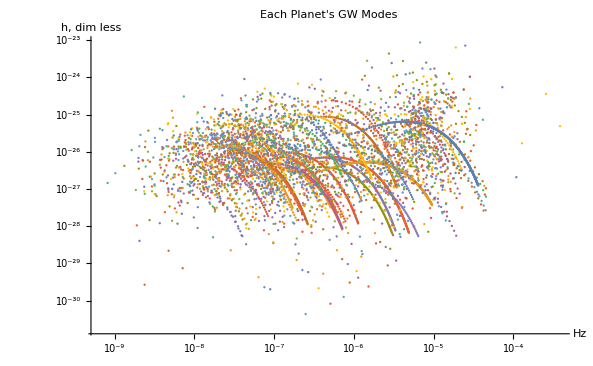

```mathematica
ListLogLogPlot[allEccList,
PlotLabel->"Each Planet's GW Modes",
AxesLabel->{"Hz", "h, dim less"}
]
```

## Plot e vs f_orb, for detection want high eccentricity but also high orbital frequency.

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
(* orbital period is in days *)
listEvF = Table[
{1.0/(fdata[[ii, cols["pl_orbper"] ]]*24.0*3600.0),fdata[[ii, cols["pl_orbeccen"] ]]},
{ii, 1, Length[fdata]}];
```

```mathematica
{Length[listEvF]}
```

{880}

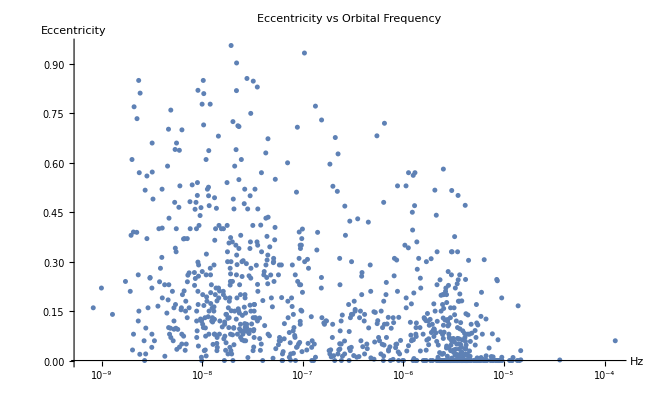

```mathematica
ListLogLinearPlot[listEvF,
PlotLabel->"Eccentricity vs Orbital Frequency",
AxesLabel->{"Hz", "Eccentricity"}
]
```

### Plot Nmax(e) vs Frequency

```mathematica
listNvF = Table[
{1.0/(fdata[[ii, cols["pl_orbper"] ]]*24.0*3600.0),aNmax[ fdata[[ii, cols["pl_orbeccen"] ]] ] },
{ii, 1, Length[fdata]}];
Length[listNvF]
```

880

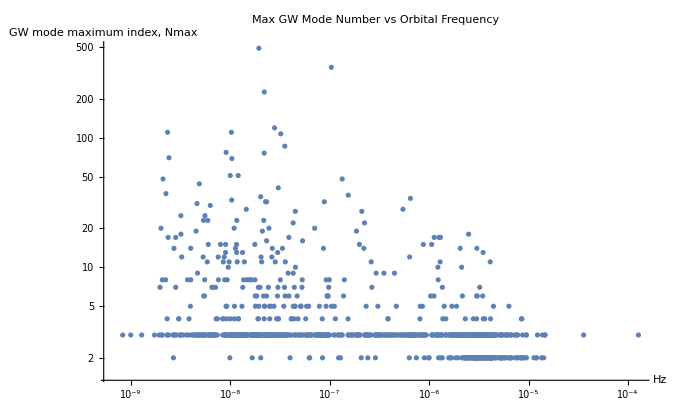

```mathematica
ListLogLogPlot[listNvF,
PlotLabel->"Max GW Mode Number vs Orbital Frequency",
AxesLabel->{"Hz", "GW mode maximum index, Nmax"}
]
```

## S_n(f) for frequency below few mHz.

```mathematica
(* Larson formula for now. *)
ssubn[freq_]:=0.1642*10^-48/freq^4
```

## Signal-to-Noise following Bill’s formula

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
getModesOnly[ eccTable, 1 ]
```

{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27},{8.99182×10^-8,8.58338×10^-28}}

```mathematica
intTime = 1.0*secsYear; (* integration time in seconds *)
SNRTable= Table[
{fdata[[ii,cols["pl_hostname"] ]]<>" "<>fdata[[ii,cols["pl_letter"] ]],
fdata[[ii, cols["pl_orbeccen"] ]], fdata[[ii, cols["pl_orbper"] ]],
Sqrt[
Module[{aa, bb},
If[Length[eccTable[[ii]] ]==1,
aa=getModesOnly[ eccTable, ii ][[1,1]];(* freq Hz *)
bb = getModesOnly[ eccTable, ii][[1, 2]];(* h dim less *)
intTime*bb^2/(2.0*ssubn[aa]),
Sum[
aa=getModesOnly[ eccTable, ii ][[jj,1]];(* freq Hz *)
bb = getModesOnly[ eccTable, ii][[jj, 2]];(* h dim less *)
intTime*bb^2/(2.0*ssubn[aa]),
{jj, 1, Length[  getModesOnly[eccTable, ii]  ]}   ]
](* end IF *)
](* end Module *)
](* end Sqrt *)
},
{ii, 1, Length[eccTable]}  ]
```

{{HD 142022 A b,0.53,1928.,5.84207×10^-13},{HD 39091 b,0.6405,2151.,4.49974×10^-12},{HD 137388 A b,0.36,330.,8.55755×10^-13},{GJ 3021 b,0.511,133.71,8.31741×10^-10},{HD 63454 b,0.,2.81805,1.92611×10^-7},{HD 212301 b,0.,2.24572,3.69061×10^-7},{HD 196067 b,0.66,3638.,4.27575×10^-13},{HD 68402 b,0.03,1103.,9.95607×10^-14},{HD 38283 b,0.41,363.2,1.56924×10^-12},{HD 131664 b,0.638,1951.,3.22299×10^-12},{HD 108341 b,0.85,1129.,4.85797×10^-11},{HD 222076 b,0.08,871.,9.12896×10^-14},{WASP-91 b,0.,2.79858,1.50891×10^-7},{HD 216437 b,0.29,1256.,2.77175×10^-13},{HD 175167 b,0.54,1290.,1.60815×10^-12},{WASP-126 b,0.18,3.2888,2.07586×10^-8},{HD 129445 b,0.7,1840.,5.08046×10^-13},{HD 111232 b,0.2,1143.,5.56201×10^-13},{HD 11977 b,0.4,711.,3.9995×10^-12},{HD 76920 b,0.856,415.4,2.96942×10^-10},{HD 76700 b,0.,3.971,2.57695×10^-8},{HD 181433 c,0.28,962.,1.22613×10^-13},{HD 181433 b,0.396,9.3743,2.06119×10^-9},{HD 181433 d,0.48,2172.,3.89177×10^-14},{HD 7199 b,0.19,615.,1.06895×10^-13},{HD 4308 b,0.,15.56,3.58653×10^-10},{HIP 63242 b,0.23,124.6,8.71622×10^-11},{WASP-119 b,0.058,2.49979,1.03083×10^-7},{HD 25171 b,0.08,1845.,1.15811×10^-14},{HIP 107773 b,0.09,144.3,2.02018×10^-11},{HD 190984 b,0.57,4885.,6.99968×10^-15},{HD 108147 b,0.53,10.8985,3.54726×10^-8},{WASP-62 b,0.21,4.41195,3.172×10^-8},{HD 65216 b,0.,572.4,4.72856×10^-13},{HD 65216 c,0.02,152.6,2.14931×10^-12},{HATS-35 b,0.306,1.821,3.40985×10^-7},{HD 219077 b,0.77,5501.,9.90101×10^-13},{Proxima Cen b,0.35,11.186,9.35555×10^-10},{HATS-34 b,0.108,2.10616,7.92627×10^-8},{NGC 4349 127 b,0.19,677.8,2.44803×10^-13},{HATS-24 b,0.242,1.3485,1.19081×10^-6},{HD 147018 c,0.133,1008.,5.0606×10^-13},{HD 147018 b,0.4686,44.236,3.05497×10^-9},{HD 224538 b,0.464,1189.1,1.15872×10^-12},{HD 196050 b,0.228,1378.,1.18843×10^-13},{HD 10180 c,0.073,5.75969,3.35617×10^-9},{HD 10180 g,0.263,604.67,3.84067×10^-14},{HD 10180 h,0.095,2205.,2.2241×10^-15},{HD 10180 f,0.119,122.744,1.78728×10^-12},{HD 10180 e,0.051,49.748,2.01776×10^-11},{HD 10180 d,0.131,16.357,2.06079×10^-10},{HD 142415 b,0.5,386.3,1.1702×10^-11},{HD 23127 b,0.44,1214.,1.26825×10^-13},{HD 40307 b,0.2,4.3123,7.03955×10^-9},{HD 40307 d,0.07,20.432,2.14075×10^-10},{HD 40307 f,0.02,51.76,9.2028×10^-12},{HD 40307 g,0.29,197.8,7.02463×10^-13},{HD 40307 c,0.06,9.6184,1.09964×10^-9},{HATS-30 b,0.096,3.17435,3.36998×10^-8},{HD 27894 d,0.389,5174.,1.36592×10^-14},{HD 27894 b,0.047,18.02,1.89472×10^-9},{HD 27894 c,0.015,36.07,7.18427×10^-11},{HD 27442 b,0.06,428.1,2.31452×10^-12},{HD 102117 b,0.121,20.8133,4.66368×10^-10},{HIP 65891 b,0.13,1084.5,2.28983×10^-13},{HD 221287 b,0.08,456.1,1.79179×10^-12},{HD 30177 c,0.22,11613.,8.56138×10^-16},{HD 30177 b,0.184,2524.4,5.02294×10^-14},{HD 101930 b,0.11,70.46,3.23887×10^-11},{HD 154857 c,0.06,3452.,6.29943×10^-15},{HD 154857 b,0.46,408.6,7.70284×10^-12},{HD 2039 b,0.715,1120.,6.94528×10^-12},{HD 215497 b,0.16,3.93404,3.87462×10^-9},{HD 215497 c,0.49,567.94,5.65985×10^-13},{HD 154672 b,0.6,163.967,4.24192×10^-10},{HD 121504 b,0.03,63.33,1.46793×10^-10},{HATS-33 b,0.08,2.54956,1.30254×10^-7},{HATS-29 b,0.158,4.60587,1.1909×10^-8},{HIP 8541 b,0.16,1560.2,3.96683×10^-14},{HD 10647 b,0.15,989.2,2.16633×10^-13},{GJ 163 c,0.099,25.6306,4.54557×10^-11},{GJ 163 d,0.373,603.951,1.16312×10^-13},{GJ 163 b,0.073,8.63182,1.24354×10^-9},{HD 23079 b,0.102,730.6,5.50895×10^-13},{HD 113538 b,0.14,663.2,1.69422×10^-13},{HD 113538 c,0.2,1818.,3.22436×10^-14},{KELT-15 b,0.,3.32944,4.33127×10^-8},{HD 160691 b,0.128,643.25,8.46287×10^-13},{HD 160691 e,0.0666,310.55,2.60254×10^-12},{HD 160691 d,0.172,9.6386,2.0559×10^-9},{HD 160691 c,0.0985,4205.8,9.06779×10^-15},{GJ 676 A b,0.323,1051.1,1.84879×10^-12},{GJ 86 b,0.0416,15.7649,5.99787×10^-8},{HD 28254 b,0.81,1116.,7.8921×10^-12},{HD 103197 b,0.,47.84,1.88436×10^-11},{HD 564 b,0.096,492.3,1.33895×10^-13},{HATS-23 b,0.114,2.16052,9.34059×10^-8},{HD 330075 b,0.,3.38773,1.17845×10^-7},{HD 85390 b,0.41,788.,6.80496×10^-14},{DENIS-P J082303.1-491201 b,0.345,246.36,6.31818×10^-11},{HATS-28 b,0.202,3.18108,2.22994×10^-8},{HD 142 c,0.21,6005.,8.64604×10^-15},{HD 142 b,0.17,349.7,3.77054×10^-12},{GJ 832 c,0.18,35.68,5.54771×10^-11},{GJ 832 b,0.08,3657.,8.30709×10^-15},{HD 216435 b,0.07,1311.,7.03266×10^-14},{HD 156411 b,0.22,842.2,1.00382×10^-13},{HD 48265 b,0.08,780.3,1.25735×10^-13},{HATS-17 b,0.029,16.2546,7.82554×10^-10},{HD 117618 b,0.42,25.827,9.87603×10^-10},{GJ 674 b,0.2,4.6938,2.3677×10^-8},{HATS-27 b,0.581,4.63704,4.69324×10^-8},{HD 152079 b,0.52,2899.,4.13356×10^-14},{HD 148156 b,0.52,1027.,2.16607×10^-13},{WASP-132 b,0.,7.13352,4.88666×10^-9},{WASP-120 b,0.057,3.61127,1.43242×10^-7},{WASP-18 b,0.0092,0.941453,0.0000436513},{WASP-19 b,0.002,0.788839,2.18948×10^-6},{Kapteyn c,0.23,121.54,2.84794×10^-12},{HD 143361 b,0.193,1046.2,1.79176×10^-13},{HD 85512 b,0.11,58.43,5.13923×10^-12},{HD 153950 b,0.34,499.4,2.74655×10^-12},{HD 83443 b,0.012,2.9857,1.22919×10^-7},{HD 159868 c,0.15,352.3,8.79989×10^-13},{HD 159868 b,0.01,1178.4,8.33546×10^-14},{HD 20794 c,0.,40.114,1.60971×10^-11},{HD 20794 d,0.,90.309,3.64221×10^-12},{HD 20794 e,0.29,147.02,1.59735×10^-12},{HD 20794 b,0.,18.315,1.45759×10^-10},{Lupus-TR-3 b,0.,3.91405,2.97937×10^-9},{HD 166724 b,0.734,5144.,1.44631×10^-13},{WASP-130 b,0.,11.551,3.1753×10^-9},{KELT-14 b,0.,1.71006,4.10105×10^-7},{WASP-129 b,0.096,5.74815,1.27966×10^-8},{HD 27631 b,0.12,2208.,1.31231×10^-14},{HD 75289 b,0.034,3.50927,1.99422×10^-7},{HIP 74890 b,0.07,822.3,1.92914×10^-13},{HD 73526 c,0.28,379.1,1.70535×10^-12},{HD 73526 b,0.29,188.9,1.20314×10^-11},{WASP-139 b,0.,5.92426,1.31171×10^-9},{WASP-5 b,0.038,1.62843,4.36886×10^-7},{HD 8535 b,0.15,1313.,2.45522×10^-14},{HD 109749 b,0.01,5.24,1.89328×10^-8},{HD 102365 b,0.34,122.1,9.72892×10^-12},{HD 162020 b,0.277,8.4282,6.89434×10^-7},{WASP-29 b,0.03,3.92273,2.44162×10^-8},{HIP 67537 b,0.59,2556.5,5.47368×10^-13},{HD 70642 b,0.034,2068.,3.16545×10^-14},{HD 6434 b,0.146,22.017,9.57029×10^-10},{WASP-7 b,0.,4.95466,3.46926×10^-8},{HD 147513 b,0.26,528.4,2.86287×10^-12},{WASP-121 b,0.,1.27493,8.58816×10^-7},{WASP-63 b,0.22,4.37809,1.10415×10^-8},{HD 4113 b,0.903,526.62,8.39112×10^-10},{HIP 105854 b,0.02,184.2,4.50463×10^-11},{HD 177565 b,0.0593,44.505,3.52018×10^-11},{HD 114613 b,0.25,3827.,4.46377×10^-15},{HD 187085 b,0.47,986.,3.29211×10^-13},{HD 208487 b,0.24,130.08,1.22827×10^-11},{NGTS-1 b,0.016,2.6473,5.57474×10^-8},{WASP-133 b,0.17,2.17642,1.11457×10^-7},{HD 117207 b,0.144,2597.,1.7065×10^-14},{HD 190647 b,0.18,1038.1,1.29968×10^-13},{HIP 67851 c,0.17,2131.8,6.2754×10^-14},{HIP 67851 b,0.05,88.9,5.7333×10^-11},{HD 114386 b,0.23,937.7,1.67328×10^-13},{WASP-8 c,0.,4323.,6.73218×10^-15},{WASP-8 b,0.31,8.15872,6.30235×10^-8},{GJ 667 C f,0.03,39.026,9.82697×10^-12},{GJ 667 C e,0.02,62.24,2.8132×10^-12},{GJ 667 C c,0.02,28.14,3.55775×10^-11},{GJ 667 C b,0.13,7.2004,2.2906×10^-9},{GJ 667 C g,0.08,256.2,1.17975×10^-13},{WASP-66 b,0.11,4.08605,5.81472×10^-8},{HD 16417 b,0.2,17.24,5.9246×10^-10},{HD 73267 b,0.256,1260.,1.40711×10^-13},{WASP-94 A b,0.13,3.95019,2.98251×10^-8},{WASP-94 B b,0.,2.00839,1.88757×10^-7},{HD 50499 b,0.23,2482.7,1.51934×10^-14},{HATS-53 b,0.33,3.85378,1.87738×10^-8},{HD 20868 b,0.75,380.85,8.7426×10^-11},{HD 93083 b,0.14,143.58,6.37209×10^-12},{HD 147873 b,0.207,116.596,7.39023×10^-11},{HD 147873 c,0.23,491.54,7.39961×10^-13},{HD 181720 b,0.26,956.,4.18226×10^-14},{WASP-123 b,0.,2.97764,7.84317×10^-8},{WASP-64 b,0.,1.57329,3.3285×10^-7},{GJ 433 b,0.08,7.3709,1.93779×10^-9},{HD 47536 b,0.2,712.13,2.10382×10^-13},{HD 114729 b,0.167,1114.,7.5394×10^-14},{HD 205739 b,0.27,279.8,2.69799×10^-12},{GJ 3341 b,0.31,14.207,2.99179×10^-10},{HATS-52 b,0.246,1.36665,8.12441×10^-7},{GJ 3634 b,0.08,2.64561,1.87346×10^-8},{WASP-124 b,0.017,3.37265,1.76314×10^-8},{WASP-41 b,0.026,3.0524,8.00421×10^-8},{WASP-41 c,0.294,421.,1.04752×10^-12},{WASP-79 b,0.,3.66239,3.9261×10^-8},{WASP-131 b,0.,5.32202,4.02442×10^-9},{WASP-72 b,0.,2.21674,2.09415×10^-7},{OGLE-2006-BLG-109L c,0.15,4927.5,6.06591×10^-18},{HD 73256 b,0.029,2.54858,1.36981×10^-6},{HATS-16 b,0.,2.6865,9.13522×10^-8},{HD 165155 b,0.2,434.5,1.65034×10^-12},{HD 43197 b,0.83,327.8,1.40361×10^-10},{HD 169830 b,0.31,225.62,3.42268×10^-11},{HD 169830 c,0.33,2102.,1.3933×10^-13},{HD 90156 b,0.31,49.77,4.41019×10^-11},{HATS-22 b,0.079,4.72281,5.71869×10^-8},{HATS-18 b,0.166,0.837843,1.8994×10^-6},{HATS-51 b,0.33,3.34887,5.26218×10^-8},{HD 20782 b,0.956,597.065,8.79607×10^-9},{HATS-26 b,0.245,3.30239,1.73541×10^-8},{HD 164604 b,0.24,606.4,9.80244×10^-13},{HD 30669 b,0.18,1684.,7.48069×10^-15},{HD 171238 b,0.4,1523.,1.93652×10^-13},{WASP-17 b,0.028,3.73544,1.34535×10^-8},{HD 133131 A b,0.33,649.,6.79792×10^-13},{HD 133131 A c,0.49,3568.,5.28728×10^-15},{HD 133131 B b,0.61,5769.,2.09861×10^-14},{HD 47186 c,0.249,1353.6,2.00937×10^-14},{HD 47186 b,0.038,4.0845,1.35662×10^-8},{HD 145377 b,0.307,103.95,3.00469×10^-10},{HD 192310 c,0.32,525.8,2.78364×10^-13},{HD 192310 b,0.13,74.72,1.90262×10^-11},{PSR J2322-2650 b,0.0017,0.322964,0.0000281842},{HD 33283 b,0.48,18.179,3.31367×10^-9},{HD 216770 b,0.37,118.45,4.06318×10^-11},{HD 4208 b,0.052,828.,1.16185×10^-13},{HATS-13 b,0.181,3.04405,2.18552×10^-8},{HATS-50 b,0.516,3.8297,3.66024×10^-8},{WASP-61 b,0.26,3.8559,6.87044×10^-8},{HD 207832 b,0.13,161.97,4.38216×10^-12},{HD 207832 c,0.27,1155.7,4.51357×10^-14},{HD 128356 b,0.57,298.2,1.18923×10^-11},{HATS-8 b,0.376,3.58389,5.29831×10^-9},{HATS-14 b,0.142,2.76676,4.89558×10^-8},{HD 77338 b,0.09,5.7361,3.57454×10^-9},{HD 134987 b,0.233,258.19,1.22546×10^-11},{HD 134987 c,0.12,5000.,2.00863×10^-15},{GJ 3293 e,0.21,13.2543,1.4973×10^-10},{GJ 3293 d,0.12,48.1345,9.60851×10^-12},{GJ 3293 c,0.11,122.62,2.16757×10^-12},{GJ 3293 b,0.06,30.5987,9.13808×10^-11},{HATS-3 b,0.,3.54785,2.81824×10^-8},{HATS-31 b,0.233,3.37796,1.89653×10^-8},{HD 30856 b,0.117,912.,1.307×10^-13},{HD 179949 b,0.022,3.09251,5.82734×10^-7},{HD 4732 c,0.23,2732.,1.71957×10^-14},{HD 4732 b,0.13,360.2,3.277×10^-12},{HD 86226 b,0.15,1695.,2.00125×10^-14},{HD 98219 b,0.112,436.9,4.43908×10^-13},{WASP-142 b,0.,2.05287,5.49495×10^-8},{WASP-20 b,0.,4.89963,7.40837×10^-9},{WASP-34 b,0.038,4.31768,3.04007×10^-8},{HATS-25 b,0.176,4.29864,1.0136×10^-8},{HD 181342 b,0.1,562.1,6.22734×10^-13},{HD 180902 b,0.09,479.,4.19526×10^-13},{GJ 317 b,0.11,692.,8.39654×10^-13},{HATS-1 b,0.12,3.44646,7.86089×10^-8},{HD 98649 b,0.85,4951.,2.51987×10^-12},{HATS-36 b,0.105,4.17524,2.85668×10^-8},{HATS-2 b,0.,1.35413,4.66041×10^-7},{HATS-4 b,0.013,2.51673,8.28128×10^-8},{HIP 5158 c,0.14,9017.76,3.10996×10^-15},{HIP 5158 b,0.52,345.72,1.00691×10^-11},{HD 224693 b,0.05,26.73,4.53563×10^-10},{HD 60532 b,0.26,201.9,2.01136×10^-11},{HD 60532 c,0.03,600.1,1.5497×10^-12},{HATS-10 b,0.501,3.31285,9.07236×10^-8},{WASP-78 b,0.,2.17518,5.81028×10^-8},{HD 95872 b,0.06,4375.,3.51787×10^-14},{HD 204313 b,0.0946,2024.1,4.58632×10^-14},{HD 204313 c,0.155,34.905,3.37839×10^-11},{HATS-5 b,0.019,4.76339,4.26684×10^-9},{HATS-32 b,0.471,2.81265,1.19264×10^-7},{HD 204941 b,0.37,1733.,1.64702×10^-14},{HD 18742 b,0.12,772.,2.02465×10^-13},{HD 202206 c,0.267,1383.4,1.25994×10^-13},{HD 202206 b,0.435,255.87,2.01989×10^-10},{HD 155233 b,0.04,818.8,2.8299×10^-13},{HD 220689 b,0.16,2209.,1.08229×10^-14},{WASP-140 b,0.047,2.23598,4.65384×10^-7},{HD 104067 b,0.,55.806,5.14413×10^-11},{WASP-67 b,0.2,4.61442,1.14746×10^-8},{HD 1666 b,0.63,270.,1.30463×10^-10},{HD 9174 b,0.12,1179.,3.24016×10^-14},{HD 11506 b,0.37,1627.5,3.05611×10^-13},{HD 11506 c,0.24,223.6,2.43084×10^-12},{HATS-15 b,0.126,1.74749,2.26747×10^-7},{HD 156846 b,0.84785,359.555,4.05565×10^-9},{WASP-83 b,0.,4.97125,4.5779×10^-9},{7 CMa b,0.22,796.,1.23499×10^-12},{WASP-31 b,0.,3.40591,1.70749×10^-8},{HATS-6 b,0.,3.32527,1.8255×10^-8},{HD 141937 b,0.41,653.22,9.83888×10^-12},{61 Vir d,0.35,123.01,1.68633×10^-11},{61 Vir b,0.12,4.215,1.32785×10^-8},{61 Vir c,0.14,38.021,1.3884×10^-10},{K2-139 b,0.12,28.3824,1.06724×10^-10},{HD 125612 b,0.46,559.4,4.2443×10^-12},{HD 125612 d,0.28,3008.,4.13418×10^-14},{HD 125612 c,0.27,4.1547,1.60599×10^-8},{HD 86950 b,0.17,1270.,5.94067×10^-14},{HD 212771 b,0.111,373.3,5.65632×10^-13},{WASP-141 b,0.,3.31065,6.87407×10^-8},{YZ Cet b,0.,1.96876,8.48528×10^-9},{YZ Cet d,0.129,4.65627,1.48974×10^-9},{YZ Cet c,0.04,3.06008,3.46641×10^-9},{WASP-49 b,0.,2.78174,4.28771×10^-8},{GJ 3138 d,0.32,257.8,2.21153×10^-13},{GJ 3138 b,0.19,1.22003,3.44712×10^-8},{GJ 3138 c,0.11,5.974,1.0113×10^-9},{BD-17 63 b,0.54,655.6,8.74046×10^-12},{tau Cet e,0.18,162.87,1.38307×10^-12},{tau Cet f,0.16,636.13,3.53981×10^-14},{tau Cet h,0.23,49.41,1.66719×10^-11},{tau Cet g,0.06,20.,1.36852×10^-10},{LHS 1140 b,0.29,24.7371,5.68932×10^-11},{WASP-26 b,0.,2.7566,9.05079×10^-8},{HD 33844 c,0.13,916.,1.12902×10^-13},{HD 33844 b,0.15,551.4,5.02551×10^-13},{PSR J1719-1438 b,0.06,0.0907063,0.00024401},{HD 72892 b,0.423,39.475,5.10621×10^-9},{GJ 876 e,0.055,124.26,3.958×10^-12},{GJ 876 c,0.25591,30.0881,4.35935×10^-9},{GJ 876 b,0.0324,61.1166,1.28212×10^-9},{GJ 876 d,0.207,1.93778,1.52165×10^-7},{HD 33142 b,0.12,326.6,8.38643×10^-13},{BD-13 2130 b,0.21,714.3,2.42299×10^-13},{WASP-70 A b,0.,3.71302,2.40895×10^-8},{Wolf 1061 d,0.55,217.21,3.94109×10^-12},{Wolf 1061 c,0.11,17.8719,1.67244×10^-10},{Wolf 1061 b,0.15,4.8869,3.17749×10^-9},{HD 69830 c,0.13,31.56,9.41797×10^-11},{HD 69830 b,0.1,8.667,2.44609×10^-9},{HD 69830 d,0.07,197.,1.00367×10^-12},{HD 82943 b,0.162,441.47,2.45795×10^-12},{HD 82943 c,0.3663,220.078,4.33453×10^-11},{HD 103774 b,0.09,5.8881,2.47019×10^-8},{WASP-47 e,0.03,0.789636,8.94464×10^-8},{WASP-47 d,0.006,9.095,2.44518×10^-10},{WASP-47 c,0.36,580.7,3.06635×10^-13},{WASP-47 b,0.0028,4.16071,4.59401×10^-8},{HD 168746 b,0.107,6.404,1.31278×10^-8},{BD-11 4672 b,0.05,1667.,1.078×10^-14},{HD 109271 b,0.25,7.8543,1.95968×10^-9},{HD 109271 c,0.15,30.93,5.33252×10^-11},{HD 176986 b,0.066,6.4898,1.27565×10^-9},{HD 176986 c,0.111,16.8191,1.71774×10^-10},{WASP-50 b,0.009,1.9551,3.0325×10^-7},{BD-10 3166 b,0.019,3.48777,6.32383×10^-8},{HD 44219 b,0.61,472.3,3.73733×10^-12},{WASP-75 b,0.,2.48419,1.21843×10^-7},{HD 28185 b,0.092,385.9,5.84331×10^-12},{HD 96167 b,0.71,498.9,8.42909×10^-12},{HD 11964 c,0.3,37.91,9.67291×10^-11},{HD 11964 b,0.041,1945.,1.05475×10^-14},{WASP-43 b,0.,0.813475,8.31036×10^-6},{nu Oph c,0.165,3186.,2.12721×10^-13},{nu Oph b,0.1256,530.32,1.87796×10^-11},{K2-140 b,0.12,6.5693,1.24887×10^-8},{HD 168443 b,0.52883,58.1125,9.43699×10^-9},{HD 168443 c,0.2113,1749.83,4.11587×10^-13},{BD-08 2823 c,0.19,237.6,1.1471×10^-12},{BD-08 2823 b,0.15,5.6,3.18251×10^-9},{HD 106270 b,0.402,2890.,1.0009×10^-13},{eps Eri b,0.702,2502.,4.00218×10^-12},{KELT-11 b,0.,4.73653,1.23377×10^-8},{91 Aqr b,0.027,181.4,2.60801×10^-11},{HD 38801 b,0.,696.3,1.08105×10^-12},{HD 1690 b,0.64,533.,3.0908×10^-10},{HD 6718 b,0.1,2496.,8.03679×10^-15},{HD 1461 b,0.172,5.77152,3.08709×10^-9},{HD 1461 c,0.305,13.5052,4.66516×10^-10},{HD 110014 b,0.462,835.477,6.21606×10^-12},{GJ 581 e,0.,3.149,5.82293×10^-9},{GJ 581 b,0.,5.3686,1.26085×10^-8},{GJ 581 c,0.,12.914,4.41673×10^-10},{HD 210277 b,0.476,442.19,9.03279×10^-12},{HD 206610 b,0.229,610.,2.39275×10^-13},{HD 106515 A b,0.572,3630.,2.71716×10^-13},{WASP-77 A b,0.,1.36003,2.57176×10^-6},{GJ 3323 b,0.23,5.3636,1.59711×10^-9},{GJ 3323 c,0.17,40.54,7.57659×10^-12},{CoRoT-17 b,0.,3.7681,2.85342×10^-8},{CoRoT-16 b,0.33,5.35227,5.65817×10^-9},{BD-06 1339 b,0.,3.8728,8.8292×10^-9},{BD-06 1339 c,0.31,125.94,1.09533×10^-11},{HD 222582 b,0.725,572.38,1.14501×10^-10},{HD 2638 b,0.,3.4442,9.28693×10^-8},{HD 30562 b,0.778,1159.2,1.1497×10^-11},{CoRoT-14 b,0.,1.51214,6.17316×10^-7},{HD 52265 b,0.35,119.6,9.66918×10^-11},{HD 126614 b,0.41,1244.,3.90123×10^-14},{WASP-69 b,0.,3.86814,3.84709×10^-8},{CoRoT-13 b,0.,4.03519,9.76536×10^-9},{WASP-106 b,0.,9.28972,6.14112×10^-9},{HD 7449 b,0.82,1275.,9.61951×10^-12},{TRAPPIST-1 d,0.07,4.04961,1.52344×10^-10},{TRAPPIST-1 e,0.085,6.09962,7.88371×10^-11},{TRAPPIST-1 c,0.083,2.42182,2.05876×10^-9},{TRAPPIST-1 b,0.081,1.51087,4.43685×10^-9},{TRAPPIST-1 g,0.061,12.3529,2.51834×10^-11},{TRAPPIST-1 f,0.063,9.20669,2.79516×10^-11},{HD 100777 b,0.36,383.7,2.49454×10^-12},{GJ 849 b,0.05,1845.,3.97523×10^-14},{HD 86081 b,0.008,2.1375,7.23941×10^-7},{CoRoT-24 b,0.,5.1134,1.13704×10^-10},{CoRoT-24 c,0.,11.759,5.92743×10^-11},{HD 16141 b,0.252,75.523,3.83857×10^-11},{HD 111998 b,0.03,825.9,7.97242×10^-13},{WASP-39 b,0.,4.05526,8.49753×10^-9},{81 Cet b,0.206,952.7,4.71635×10^-13},{HAT-P-45 b,0.049,3.12899,5.13151×10^-8},{HD 107148 b,0.05,48.056,4.52956×10^-11},{HAT-P-46 b,0.123,4.46313,1.2579×10^-8},{HD 103720 b,0.086,4.5557,7.29487×10^-8},{GJ 536 b,0.08,8.7076,1.10366×10^-9},{HD 179079 b,0.115,14.476,4.14598×10^-10},{HD 96063 b,0.03,361.1,3.3371×10^-13},{HD 217107 b,0.1267,7.12682,1.20549×10^-7},{HD 217107 c,0.517,4270.,5.50495×10^-14},{HD 290327 b,0.08,2443.,1.25645×10^-14},{HD 114783 b,0.144,493.7,1.13995×10^-12},{HD 218566 b,0.3,225.7,2.07708×10^-12},{HD 92788 b,0.35,325.,1.83506×10^-11},{WASP-80 b,0.002,3.06785,9.70448×10^-8},{WASP-28 b,0.,3.40883,2.59937×10^-8},{HD 72659 b,0.22,3658.,8.16989×10^-15},{HD 99109 b,0.09,439.3,2.33639×10^-13},{CoRoT-12 b,0.07,2.82804,1.68823×10^-8},{HD 19994 b,0.063,466.2,1.82808×10^-12},{HD 66428 b,0.465,1973.,1.38247×10^-13},{WASP-74 b,0.,2.13775,4.16717×10^-7},{CoRoT-7 c,0.,3.698,1.43154×10^-9},{CoRoT-7 b,0.,0.853592,5.20687×10^-8},{75 Cet b,0.117,691.9,5.94147×10^-13},{24 Sex b,0.09,452.8,9.70143×10^-13},{24 Sex c,0.29,883.,1.28775×10^-13},{HD 192263 b,0.008,24.3587,1.98285×10^-9},{HIP 97233 b,0.61,1058.8,1.08748×10^-11},{HD 217786 b,0.4,1319.,1.20015×10^-12},{HD 130322 b,0.029,10.7087,2.03064×10^-8},{CoRoT-19 b,0.047,3.89713,1.35008×10^-8},{WASP-54 b,0.067,3.69364,3.53991×10^-8},{CoRoT-18 b,0.08,1.90007,2.2798×10^-7},{HD 164509 b,0.26,282.4,1.51328×10^-12},{CoRoT-20 b,0.562,9.24285,3.01807×10^-8},{HIP 116454 b,0.205,9.1205,3.53703×10^-10},{CoRoT-10 b,0.53,13.2406,1.79747×10^-8},{WASP-71 b,0.,2.90367,1.56598×10^-7},{HD 5319 b,0.02,641.,2.04923×10^-13},{HD 5319 c,0.15,886.,6.68869×10^-14},{Ross 128 b,0.116,9.8658,3.13845×10^-10},{WASP-37 b,0.,3.57747,5.17277×10^-8},{HD 38529 b,0.257,14.3098,1.09495×10^-8},{HD 38529 c,0.341,2140.2,4.10754×10^-13},{CoRoT-2 b,0.0143,1.74299,1.18081×10^-6},{CoRoT-8 b,0.,6.21229,1.28133×10^-9},{GJ 328 b,0.37,4100.,1.74984×10^-14},{HD 95089 b,0.157,507.,2.09299×10^-13},{HD 70573 b,0.4,851.8,2.15682×10^-12},{WASP-84 b,0.,8.52349,4.99401×10^-9},{WASP-82 b,0.,2.70578,1.85853×10^-7},{HD 149143 b,0.08,4.088,1.69642×10^-7},{ome Ser b,0.106,277.02,3.37106×10^-12},{HD 66141 b,0.07,480.5,2.07389×10^-12},{WASP-156 b,0.007,3.83617,6.89997×10^-9},{WASP-76 b,0.,1.80989,6.20632×10^-7},{BD+03 2562 b,0.2,481.9,6.48581×10^-14},{HD 12484 b,0.07,58.83,3.61717×10^-10},{HD 99492 b,0.07,17.054,2.11233×10^-10},{HD 102329 b,0.211,778.1,5.63998×10^-13},{HD 200964 b,0.04,613.8,3.91242×10^-13},{HD 200964 c,0.181,825.,1.05763×10^-13},{HAT-P-26 b,0.124,4.23452,2.87741×10^-9},{HD 175541 b,0.33,297.3,1.23877×10^-12},{CoRoT-23 b,0.16,3.6313,6.22587×10^-8},{HD 3167 b,0.,0.959641,1.05762×10^-7},{HD 3167 c,0.267,29.8454,3.66155×10^-11},{HD 3167 d,0.36,8.509,1.21178×10^-9},{HD 28678 b,0.168,387.1,6.88289×10^-13},{HD 74156 c,0.432,2473.,1.62202×10^-13},{HD 74156 b,0.627,51.645,4.46271×10^-9},{HD 192699 b,0.129,345.53,2.96897×10^-12},{HAT-P-41 b,0.,2.69405,6.41239×10^-8},{HAT-P-35 b,0.025,3.64671,2.23285×10^-8},{GJ 273 b,0.1,18.6498,1.43751×10^-10},{GJ 273 c,0.17,4.7234,2.56668×10^-9},{HD 46375 b,0.063,3.02357,1.06772×10^-7},{CoRoT-28 b,0.047,5.20851,3.06991×10^-9},{HD 159243 b,0.02,12.62,6.3856×10^-9},{HD 159243 c,0.075,248.4,4.03443×10^-12},{HAT-P-30 b,0.035,2.8106,8.38006×10^-8},{CoRoT-11 b,0.,2.99433,8.37348×10^-8},{HAT-P-27 b,0.,3.03958,4.72463×10^-8},{HD 37605 b,0.6767,55.0131,1.2346×10^-8},{HD 37605 c,0.013,2720.,1.67804×10^-14},{HAT-P-42 b,0.,4.64188,1.3402×10^-8},{CoRoT-9 b,0.133,95.2727,3.34646×10^-12},{CoRoT-22 b,0.077,9.75598,5.16141×10^-11},{GJ 179 b,0.21,2288.,1.53353×10^-14},{CoRoT-29 b,0.082,2.85057,2.25905×10^-8},{CoRoT-25 b,0.,4.86069,1.29397×10^-9},{HD 42618 b,0.19,149.61,1.19234×10^-12},{HD 171028 b,0.59,550.,3.93647×10^-12},{CoRoT-26 b,0.,4.20474,2.17626×10^-9},{WASP-90 b,0.,3.91624,2.00939×10^-8},{HD 34445 f,0.031,676.8,2.42746×10^-14},{HD 34445 g,0.032,5700.,2.68782×10^-16},{HD 34445 e,0.09,49.175,1.25151×10^-11},{HD 34445 d,0.027,117.87,2.07832×10^-12},{HD 34445 c,0.036,214.67,7.33009×10^-13},{HD 34445 b,0.014,1056.7,3.8947×10^-14},{WASP-104 b,0.,1.75541,6.44855×10^-7},{K2-18 c,0.47,8.962,1.62737×10^-9},{K2-18 b,0.43,32.9396,4.17077×10^-11},{HD 4313 b,0.041,356.,1.18356×10^-12},{HD 183263 b,0.3567,626.5,2.1838×10^-12},{HD 183263 c,0.239,3070.,1.58722×10^-14},{xi Aql b,0.,136.75,4.5585×10^-11},{WASP-65 b,0.,2.31142,1.5666×10^-7},{WASP-52 b,0.,1.74978,2.04611×10^-7},{bet Cnc b,0.08,605.2,1.45505×10^-12},{HD 128311 c,0.159,921.538,9.39644×10^-13},{HD 128311 b,0.303,453.019,4.94578×10^-12},{WASP-38 b,0.0314,6.87182,5.01364×10^-8},{HD 106252 b,0.482,1531.,1.03739×10^-12},{HAT-P-43 b,0.,3.33269,1.57471×10^-8},{WASP-114 b,0.012,1.54877,4.3721×10^-7},{HAT-P-57 b,0.,2.4653,2.18825×10^-7},{MASCARA-1 b,0.,2.14878,7.65281×10^-7},{18 Del b,0.08,993.3,7.82981×10^-13},{HD 45652 b,0.38,43.6,4.38115×10^-10},{GJ 3998 c,0.049,13.74,2.03416×10^-10},{GJ 3998 b,0.,2.64977,6.9489×10^-9},{HD 196885 b,0.48,1333.,1.02031×10^-12},{HD 170469 b,0.11,1145.,3.44699×10^-14},{HD 152581 b,0.074,689.,7.02425×10^-14},{HAT-P-65 b,0.304,2.60546,3.49155×10^-8},{HAT-P-50 b,0.115,3.12201,5.24953×10^-8},{HD 31253 b,0.3,466.,5.10098×10^-13},{NN Ser c,0.08,5573.55,2.52647×10^-16},{NN Ser d,0.19,2883.5,5.55627×10^-16},{HD 73534 b,0.074,1770.,1.105×10^-14},{HD 75784 b,0.13,341.7,1.29843×10^-12},{70 Vir b,0.399,116.693,1.40031×10^-9},{HD 1502 b,0.101,431.8,8.04449×10^-13},{HD 102272 b,0.05,127.58,4.22386×10^-11},{HAT-P-24 b,0.067,3.35524,2.46405×10^-8},{BD+15 2375 b,0.001,153.22,6.54426×10^-13},{BD+14 4559 b,0.29,268.94,5.27551×10^-12},{GJ 3470 b,0.017,3.33665,2.16972×10^-8},{HD 142245 b,0.09,1299.,4.20517×10^-14},{BD+15 2940 b,0.26,137.48,6.80511×10^-12},{HD 210702 b,0.094,354.8,2.25744×10^-12},{HD 231701 b,0.1,141.6,8.07918×10^-12},{alf Tau b,0.1,628.96,4.40416×10^-12},{HAT-P-23 b,0.,1.21288,1.02338×10^-6},{HD 59686 A b,0.05,299.36,8.59087×10^-12},{tau Boo b,0.011,3.31246,3.89922×10^-6},{HD 24040 b,0.04,3668.,9.40219×10^-15},{HD 114762 b,0.3354,83.9151,1.33004×10^-9},{11 Com b,0.231,326.03,2.8182×10^-11},{HAT-P-39 b,0.,3.54387,1.22679×10^-8},{HD 87646 b,0.05,13.481,5.26056×10^-8},{HAT-P-34 b,0.441,5.45265,2.34729×10^-7},{HD 88133 b,0.05,3.41487,1.81907×10^-7},{HD 131496 b,0.163,883.,1.3474×10^-13},{WASP-21 b,0.,4.32248,6.04685×10^-9},{HD 219828 c,0.8115,4791.,1.70665×10^-12},{HD 219828 b,0.059,3.83489,1.45739×10^-8},{HD 195019 b,0.0138,18.2013,1.37893×10^-8},{HD 285968 b,0.,8.7836,1.32591×10^-9},{HD 208897 b,0.07,352.7,1.31407×10^-12},{eps Tau b,0.151,594.9,4.5107×10^-12},{TYC 1422-614-1 b,0.06,198.4,8.97852×10^-13},{TYC 1422-614-1 c,0.048,559.3,2.29698×10^-13},{gam 1 Leo b,0.144,428.5,9.16141×10^-12},{BD+20 2457 c,0.18,621.99,1.6901×10^-12},{BD+20 2457 b,0.15,379.63,1.02281×10^-11},{HD 10697 b,0.099,1075.2,5.6227×10^-13},{HD 5891 b,0.066,177.11,2.60052×10^-11},{HD 81040 b,0.526,1001.7,4.72411×10^-12},{BD+20 1790 b,0.22,7.78287,3.16318×10^-7},{HD 100655 b,0.085,157.57,1.00367×10^-11},{HD 4203 c,0.24,6700.,9.37785×10^-16},{HD 4203 b,0.52,437.05,5.15783×10^-12},{HD 37124 d,0.16,1862.,1.32583×10^-14},{HD 37124 c,0.125,885.5,8.50004×10^-14},{HD 37124 b,0.054,154.378,8.38774×10^-12},{51 Peg b,0.013,4.23079,2.2542×10^-7},{HIP 14810 d,0.173,952.,4.60233×10^-14},{HIP 14810 b,0.1427,6.67386,1.66201×10^-7},{HIP 14810 c,0.164,147.73,1.47361×10^-11},{HD 208527 b,0.08,875.5,1.77948×10^-13},{HD 3651 b,0.596,62.218,1.22289×10^-9},{WASP-14 b,0.091,2.24375,1.95305×10^-6},{HD 108863 b,0.06,443.4,7.80807×10^-13},{HD 111591 b,0.26,1056.4,2.93601×10^-13},{HD 108874 c,0.239,1624.,1.60001×10^-14},{HD 108874 b,0.082,395.8,7.02637×10^-13},{WASP-56 b,0.,4.6171,1.18225×10^-8},{alf Ari b,0.25,380.8,7.06034×10^-12},{HD 14067 b,0.533,1455.,7.40634×10^-13},{KELT-8 b,0.035,3.24406,5.61875×10^-8},{HD 50554 b,0.501,1293.,1.62678×10^-12},{HAT-P-20 b,0.015,2.87532,1.60272×10^-6},{30 Ari B b,0.289,335.1,3.05298×10^-11},{HD 116029 b,0.054,670.,2.18977×10^-13},{WASP-59 b,0.1,7.91959,7.47215×10^-9},{HAT-P-25 b,0.032,3.65284,1.87931×10^-8},{HD 12661 c,0.031,1708.,3.68111×10^-14},{HD 12661 b,0.3768,262.709,1.93231×10^-11},{KELT-4 A b,0.,2.98959,8.02139×10^-8},{HD 97658 b,0.063,9.4909,7.61045×10^-10},{HAT-P-55 b,0.139,3.58525,1.44518×10^-8},{GJ 649 b,0.3,598.3,5.10953×10^-13},{HD 177830 b,0.009,406.6,1.10369×10^-12},{HD 177830 c,0.3,110.9,7.21088×10^-12},{mu Leo b,0.09,357.8,4.39146×10^-12},{HD 164922 c,0.22,75.765,6.57564×10^-12},{HD 164922 b,0.126,1201.1,2.97158×10^-14},{HD 32963 b,0.07,2372.,6.12835×10^-15},{V0391 Peg b,0.,1170.,3.09834×10^-15},{HAT-P-31 b,0.245,5.00543,7.19355×10^-8},{HAT-P-49 b,0.,2.69155,1.55997×10^-7},{GJ 436 b,0.13827,2.64388,1.10477×10^-7},{HD 145457 b,0.112,176.3,1.25008×10^-11},{eps CrB b,0.11,417.9,4.83174×10^-12},{HAT-P-56 b,0.246,2.79083,2.67964×10^-7},{HD 158038 b,0.291,521.,7.13678×10^-13},{HD 113996 b,0.28,610.2,1.66461×10^-12},{HD 62509 b,0.02,589.64,6.13515×10^-12},{HD 188015 b,0.137,461.2,8.46543×10^-13},{XO-1 b,0.,3.94151,4.43442×10^-8},{55 Cnc d,0.019,4825.,1.26775×10^-14},{55 Cnc b,0.0034,14.6515,1.40299×10^-8},{55 Cnc f,0.305,262.,2.2484×10^-12},{55 Cnc c,0.02,44.4175,1.5085×10^-10},{HD 185269 b,0.3,6.838,8.46286×10^-8},{HD 8574 b,0.297,227.,1.41001×10^-11},{HAT-P-52 b,0.047,2.7536,4.16258×10^-8},{HIP 109600 b,0.163,232.08,7.63571×10^-12},{HD 9446 b,0.2,30.052,6.0241×10^-10},{HD 9446 c,0.06,192.9,8.79177×10^-12},{HD 164595 b,0.088,40.,2.97187×10^-11},{omi CrB b,0.191,187.83,9.76634×10^-12},{WASP-135 b,0.,1.40138,7.86646×10^-7},{HD 190360 b,0.313,2915.,3.34966×10^-14},{HD 190360 c,0.237,17.111,7.35446×10^-10},{tau Gem b,0.031,305.5,2.88173×10^-11},{HD 17674 b,0.13,623.8,2.38851×10^-13},{HAT-P-17 b,0.342,10.3385,8.14846×10^-9},{HAT-P-17 c,0.39,5584.,4.1886×10^-15},{KELT-6 c,0.21,1276.,3.86231×10^-14},{KELT-6 b,0.029,7.84558,2.81884×10^-9},{WASP-11 b,0.,3.72247,3.46735×10^-8},{KELT-2 A b,0.,4.11379,1.03843×10^-7},{HD 1605 c,0.098,2111.,2.26183×10^-14},{HD 1605 b,0.078,577.9,1.93615×10^-13},{WASP-60 b,0.,4.305,8.48959×10^-9},{HD 67087 c,0.76,2374.,1.48107×10^-12},{HD 67087 b,0.17,352.2,2.59511×10^-12},{KELT-16 b,0.,0.968995,2.63242×10^-6},{HD 214823 b,0.154,1877.,1.56624×10^-13},{HD 22781 b,0.8191,528.07,1.10272×10^-9},{HD 180314 b,0.257,396.03,2.20255×10^-11},{WASP-1 b,0.,2.51995,6.33711×10^-8},{HAT-P-38 b,0.067,4.64038,5.33757×10^-9},{HAT-P-51 b,0.123,4.21803,4.88619×10^-9},{HAT-P-18 b,0.084,5.50802,3.46437×10^-9},{HD 75898 b,0.1,418.2,1.25489×10^-12},{rho CrB b,0.0373,39.8458,9.43411×10^-10},{rho CrB c,0.052,102.54,5.78277×10^-12},{KELT-7 b,0.,2.73477,2.75387×10^-7},{HAT-P-33 b,0.,3.47447,2.72361×10^-8},{WASP-13 b,0.,4.35301,1.99173×10^-8},{HD 5608 b,0.19,792.6,2.53574×10^-13},{HD 42012 b,0.2,857.5,2.21938×10^-13},{HD 187123 c,0.252,3810.,5.33865×10^-15},{HD 187123 b,0.0103,3.09658,1.49402×10^-7},{HD 178911 B b,0.114,71.484,5.85272×10^-10},{HAT-P-19 b,0.067,4.00878,9.55515×10^-9},{HAT-P-28 b,0.051,3.25722,2.14785×10^-8},{HD 82886 b,0.066,705.,8.25336×10^-14},{HD 5583 b,0.076,139.35,1.6163×10^-11},{HAT-P-8 b,0.,3.07638,8.67419×10^-8},{kap CrB b,0.044,1261.94,1.05936×10^-13},{WASP-3 b,0.003,1.84684,6.23497×10^-7},{HAT-P-4 b,0.,3.05654,3.93842×10^-8},{WTS-1 b,0.1,3.35206,1.82584×10^-8},{HD 173416 b,0.21,323.6,2.60543×10^-12},{KELT-12 b,0.,5.03162,1.48391×10^-8},{Kepler-75 b,0.57,8.88491,7.80002×10^-8},{HAT-P-5 b,0.,2.78849,6.85374×10^-8},{WTS-2 b,0.,1.01871,2.86651×10^-7},{HAT-P-9 b,0.,3.92289,1.51963×10^-8},{TrES-4 b,0.016,3.55393,1.34432×10^-8},{TrES-3 b,0.,1.30619,1.20495×10^-6},{HAT-P-14 b,0.107,4.62767,7.77373×10^-8},{Kepler-9 c,0.13,38.91,6.07418×10^-12},{Kepler-9 b,0.15,19.24,6.17788×10^-11},{Kepler-21 b,0.02,2.78578,3.81627×10^-9},{Kepler-30 d,0.022,143.344,3.69903×10^-14},{Kepler-30 b,0.042,29.3343,1.09999×10^-12},{Kepler-30 c,0.0111,60.3231,7.84446×10^-12},{HD 45350 b,0.778,963.6,1.18008×10^-11},{HAT-P-53 b,0.134,1.96162,1.28278×10^-7},{XO-5 b,0.,4.18776,3.17104×10^-8},{14 And b,0.,185.84,2.8904×10^-11},{KELT-1 b,0.0099,1.21751,0.0000224982},{HAT-P-15 b,0.19,10.8635,6.92108×10^-9},{KELT-9 b,0.,1.48112,3.04021×10^-6},{PH1 b,0.0702,138.317,3.24694×10^-13},{WASP-153 b,0.009,3.33261,1.38242×10^-8},{KELT-3 b,0.,2.70339,2.12199×10^-7},{47 UMa c,0.098,2391.,1.18919×10^-14},{47 UMa d,0.16,14002.,3.71599×10^-16},{47 UMa b,0.032,1078.,4.4686×10^-13},{HD 23596 b,0.266,1561.,2.58945×10^-13},{Kepler-425 b,0.33,3.79702,7.68424×10^-9},{Kepler-428 b,0.22,3.52563,2.27145×10^-8},{KOI-142 c,0.05628,22.3395,1.36119×10^-10},{HD 49674 b,0.087,4.94737,1.23565×10^-8},{Kepler-433 b,0.119,5.33408,7.68728×10^-9},{KOI-12 b,0.72,17.8552,1.86042×10^-7},{HAT-P-21 b,0.228,4.12448,1.46975×10^-7},{HAT-P-2 b,0.5171,5.63347,1.7929×10^-6},{Kepler-45 b,0.11,2.45524,3.26129×10^-8},{HD 43691 b,0.14,36.96,8.07385×10^-10},{HD 89744 b,0.673,256.78,8.70792×10^-10},{Kepler-74 b,0.,7.34071,7.98338×10^-10},{ups And b,0.0215,4.61703,3.17335×10^-7},{ups And d,0.2987,1276.46,1.18636×10^-12},{ups And c,0.2596,241.258,3.96934×10^-11},{HD 136418 b,0.255,464.3,8.11342×10^-13},{Kepler-539 b,0.39,125.632,8.11399×10^-12},{Kepler-539 c,0.5,1000.,7.0568×10^-14},{Kepler-11 c,0.026,13.0241,4.67855×10^-12},{Kepler-11 f,0.013,46.6888,1.04124×10^-13},{Kepler-11 e,0.012,31.9996,1.17181×10^-12},{Kepler-11 b,0.045,10.3039,6.04218×10^-12},{Kepler-11 g,0.15,118.381,1.34648×10^-13},{Kepler-11 d,0.004,22.6845,2.697×10^-12},{HD 16175 b,0.637,995.4,5.58243×10^-12},{Kepler-38 b,0.032,105.599,5.58946×10^-13},{Kepler-20 b,0.03,3.69612,9.38906×10^-10},{Kepler-20 c,0.16,10.8541,8.36939×10^-11},{Kepler-20 g,0.15,34.94,5.85852×10^-12},{HAT-P-16 b,0.036,2.77596,4.17653×10^-7},{HAT-P-6 b,0.,3.85299,4.04207×10^-8},{Kepler-46 b,0.01,33.6013,1.71827×10^-10},{Kepler-46 c,0.0146,57.011,2.61902×10^-12},{Kepler-434 b,0.131,12.8747,1.00958×10^-9},{Kepler-435 b,0.114,8.60015,5.99961×10^-10},{HAT-P-12 b,0.,3.21306,1.6339×10^-8},{Kepler-427 b,0.57,10.291,1.66932×10^-9},{HD 13931 b,0.02,4218.,2.76561×10^-15},{HD 95127 b,0.11,482.,4.06367×10^-13},{14 Her b,0.369,1773.4,4.60397×10^-13},{HD 99706 b,0.365,868.,1.93208×10^-13},{HD 40979 b,0.252,264.15,2.28857×10^-11},{HD 96127 b,0.3,647.3,3.57863×10^-13},{Kepler-77 b,0.,3.57878,7.4698×10^-9},{Kepler-34 b,0.182,288.822,6.47328×10^-15},{HAT-P-67 b,0.,4.8101,7.18506×10^-9},{HAT-P-36 b,0.063,1.32735,8.78183×10^-7},{KOI-1257 b,0.772,86.6477,2.85525×10^-10},{WASP-58 b,0.,5.01718,1.19229×10^-8},{HAT-P-40 b,0.,4.45724,9.22279×10^-9},{HD 81688 b,0.,184.02,1.41237×10^-11},{Kepler-44 b,0.066,3.24673,6.62059×10^-9},{Kepler-41 b,0.,1.85556,4.68387×10^-8},{Kepler-39 b,0.112,21.0872,1.96156×10^-9},{Kepler-423 b,0.019,2.68433,1.62285×10^-8},{Kepler-35 b,0.042,131.458,2.11287×10^-14},{Kepler-47 b,0.035,49.532,8.71919×10^-12},{Kepler-47 c,0.411,303.137,3.62421×10^-12},{WASP-113 b,0.,4.54217,8.63016×10^-9},{HD 141399 b,0.04,94.44,2.20059×10^-11},{HD 141399 e,0.26,5000.,2.50479×10^-15},{HD 141399 d,0.074,1069.8,9.28449×10^-14},{HD 141399 c,0.048,201.99,8.60683×10^-12},{HAT-P-44 b,0.044,4.30122,5.95337×10^-9},{HAT-P-44 c,0.494,872.2,2.85491×10^-13},{Kepler-40 b,0.,6.87349,1.96406×10^-9},{Kepler-17 b,0.011,1.48571,4.12911×10^-7},{Kepler-22 b,0.,289.862,4.84845×10^-14},{HAT-P-7 b,0.0016,2.20474,2.80292×10^-7},{HAT-P-3 b,0.,2.89974,7.30836×10^-8},{Kepler-117 b,0.0493,18.7959,8.87838×10^-12},{Kepler-117 c,0.0323,50.7904,1.21094×10^-11},{HAT-P-11 b,0.198,4.88782,1.02488×10^-8},{Kepler-432 b,0.5134,52.5011,4.15091×10^-10},{HIP 65407 b,0.14,28.125,3.57315×10^-10},{HIP 65407 c,0.12,67.3,6.23226×10^-11},{HD 222155 b,0.16,3999.,3.87076×10^-15},{Kepler-36 b,0.039,13.8399,8.82×10^-12},{Kepler-36 c,0.033,16.2386,1.0229×10^-11},{Kepler-426 b,0.18,3.21752,6.12257×10^-9},{Kepler-63 b,0.45,9.43415,9.15749×10^-9},{TYC 3318-01333-1 b,0.098,562.,1.07336×10^-13},{HAT-P-22 b,0.016,3.21222,3.41209×10^-7},{Kepler-4 b,0.,3.21346,2.16936×10^-9},{XO-2 S c,0.1528,120.8,9.34502×10^-12},{XO-2 S b,0.18,18.157,2.89537×10^-10},{XO-2 N b,0.006,2.61586,9.55662×10^-8},{16 Cyg B b,0.681,798.5,1.22273×10^-11},{HD 80606 b,0.9332,111.436,6.85997×10^-7},{WASP-92 b,0.,2.17467,6.60532×10^-8},{HAT-P-37 b,0.058,2.79744,5.55338×10^-8},{WASP-93 b,0.,2.73253,1.49044×10^-7},{Kepler-16 b,0.0069,228.776,4.74547×10^-13},{HAT-P-29 b,0.095,5.72319,8.73486×10^-9},{HD 191806 b,0.259,1606.3,1.84601×10^-13},{GJ 3942 b,0.121,6.905,1.95812×10^-9},{HD 118203 b,0.309,6.1335,1.43122×10^-7},{HD 139357 b,0.1,1125.7,2.34151×10^-13},{HAT-P-66 b,0.09,2.97209,1.76681×10^-8},{HD 167042 b,0.089,420.77,1.22116×10^-12},{GJ 625 b,0.13,14.628,1.68591×10^-10},{HD 2952 b,0.129,311.6,2.23051×10^-12},{HD 163607 c,0.12,1314.,5.81759×10^-14},{HD 163607 b,0.73,75.29,1.72296×10^-9},{HD 219415 b,0.4,2093.3,8.66676×10^-15},{HD 220842 b,0.404,218.47,3.41399×10^-11},{HD 240210 b,0.15,501.75,7.28364×10^-13},{HD 219134 g,0.,94.2,7.7273×10^-12},{HD 219134 h,0.06,2247.,1.69804×10^-14},{HD 219134 f,0.148,22.717,2.67579×10^-10},{HD 219134 b,0.,3.09293,2.97849×10^-8},{HD 219134 d,0.138,46.859,8.46202×10^-11},{HD 219134 c,0.062,6.76458,3.532×10^-9},{HD 102956 b,0.048,6.495,2.39577×10^-8},{XO-3 b,0.26,3.19152,1.76655×10^-6},{HD 240237 b,0.4,745.7,5.83645×10^-13},{6 Lyn b,0.125,874.774,2.54784×10^-13},{TYC 3667-1280-1 b,0.036,26.468,9.23138×10^-10},{HIP 75458 b,0.7124,511.098,2.10446×10^-10},{HD 238914 b,0.56,4100.,1.79299×10^-14},{KELT-18 b,0.,2.87175,9.21301×10^-8},{HD 29021 b,0.459,1362.3,4.62082×10^-13},{omi UMa b,0.13,1630.,1.55492×10^-13},{HD 68988 b,0.1249,6.27711,9.19824×10^-8},{HIP 91258 b,0.024,5.0505,9.3088×10^-8},{HD 220074 b,0.14,672.1,4.47438×10^-13},{TYC 4282-00605-1 b,0.28,101.54,3.64544×10^-11},{HD 221585 b,0.123,1173.,7.69441×10^-14},{HD 156279 b,0.708,131.05,6.77532×10^-9},{HD 40956 b,0.24,578.6,1.4573×10^-12},{HD 113337 b,0.46,324.,4.58226×10^-11},{HD 35759 b,0.389,82.467,4.39193×10^-10},{4 UMa b,0.432,269.3,4.4968×10^-11},{42 Dra b,0.38,479.1,2.62247×10^-12},{HD 13908 c,0.12,931.,3.83401×10^-13},{HD 13908 b,0.02,19.382,1.73033×10^-9},{HD 147379 b,0.01,86.54,1.05623×10^-11},{GJ 687 b,0.04,38.14,1.37685×10^-10},{HD 143105 b,0.07,2.1974,1.29634×10^-6},{HD 32518 b,0.01,157.54,1.23295×10^-11},{HIP 109384 b,0.549,499.48,4.12283×10^-12},{HD 17156 b,0.6819,21.2166,1.24698×10^-7},{11 UMi b,0.08,516.22,2.43344×10^-12},{psi 1 Dra B b,0.4,3117.,3.91798×10^-14},{HD 11755 b,0.19,433.7,9.61145×10^-13},{XO-6 b,0.,3.765,4.18003×10^-8},{HD 24064 b,0.35,535.6,1.50168×10^-12},{bet UMi b,0.19,522.3,4.60173×10^-12},{HD 109246 b,0.12,68.27,5.13506×10^-11},{8 UMi b,0.06,93.4,2.47249×10^-11},{HD 7924 b,0.058,5.39792,5.05623×10^-9},{HD 7924 d,0.21,24.451,8.44178×10^-11},{HD 7924 c,0.098,15.299,3.00533×10^-10},{gam Cep b,0.049,903.3,6.87219×10^-13},{HD 120084 b,0.66,2082.,7.90627×10^-13},{HD 33564 b,0.34,388.,5.19313×10^-11},{HD 150706 b,0.38,5894.,9.26729×10^-15},{HD 12648 b,0.04,133.6,1.42152×10^-11}}

```mathematica
SNRTable[[1]]
```

{HD 142022 A b,0.53,1928.,5.84207×10^-13}

```mathematica
{eccTable, fdata}//Length
```

2

```mathematica
SNRTableSorted = Sort[SNRTable, #1[[4]]> #2[[4]] &];
```

```mathematica
SNRTableSorted[[1;;10]]
```

{{PSR J1719-1438 b,0.06,0.0907063,0.00024401},{WASP-18 b,0.0092,0.941453,0.0000436513},{PSR J2322-2650 b,0.0017,0.322964,0.0000281842},{KELT-1 b,0.0099,1.21751,0.0000224982},{WASP-43 b,0.,0.813475,8.31036×10^-6},{tau Boo b,0.011,3.31246,3.89922×10^-6},{KELT-9 b,0.,1.48112,3.04021×10^-6},{KELT-16 b,0.,0.968995,2.63242×10^-6},{WASP-77 A b,0.,1.36003,2.57176×10^-6},{WASP-19 b,0.002,0.788839,2.18948×10^-6}}